## Laplace Approximation

The following section sets up the equations required to compute the exact and the Laplace approximations of the conditional probabilities

ⅇ^(1/2 V (-2/O_tot-(k x)/(α O_tot)-α/(k x O_tot)) (y-(k x O_tot)/(k x+α))^2)

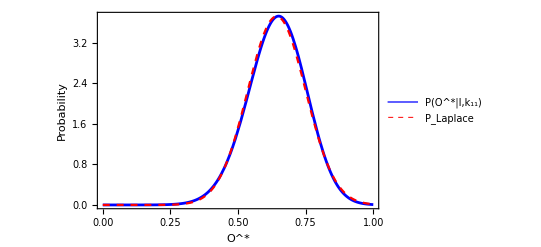

```mathematica
SetOptions[$FrontEndSession,EvaluationCompletionAction->"ShowTiming"]
(* Exact probability *)
p[y_,Inp_,k_,V_]:=ⅇ^((2 V y (Inp^2 k^2-α^2))/(-Inp k+α)^2)ⅇ^(-Log[1+((α-Inp k)y)/(Inp k Subscript[O, tot])])ⅇ^((4 Inp k Subscript[O, tot] α V)/(α-Inp k)^2 Log[1+((α-Inp k)y)/(Inp k Subscript[O, tot])]); (* I checked that this probability is the correct solution to FP equation *)
(* define f(x) and find max O_max. f(x) is the exponent in the conditional probability as V -> infinity *)
f[y_,Inp_,k_]:=(4 Inp k Subscript[O, tot] α)/(α-Inp k)^2 Log[1+((α-Inp k)y)/(Inp k Subscript[O, tot])]-(2 y (Inp k+α))/(α-Inp k)
(*Solve[D[f[y,Inp,k],y]==0,y]; *)
(* the following with the linear correction works really well *)
(*fDoublePrimeyMax[Inp_,k_]:=-(2 (α+Inp k))/(Inp  *k*  Subscript[O, tot])- Inp*k; *)
fDoublePrimeyMax[Inp_,k_]:=-2/Subscript[O, tot]-(Inp k)/(α Subscript[O, tot])-α/(Inp k Subscript[O, tot]);
(*fDoublePrimeyMax[Inp_,k_]:=-(2 (α+Inp k))/(Inp  *k*  Subscript[O, tot]);*)
fMax[Inp_,k_]:=(-2Inp k)/(α-Inp k)+(4 Inp k α Subscript[O, tot])/(α-Inp k)^2 Log[(2α)/(α-Inp k)];
Omax[Inp_,k_]:=(Inp k Subscript[O, tot])/(Inp k+α); (* location of the mean of the conditional probability *)
(* Define the laplace approximation of the exact probability *)
(* works okay for boundary near 1 *)
(*pLaplace[y_,Inp_,k_,V_]:=Exp[V(1/(2/(3*Inp))fDoublePrimeyMax[Inp,k] (y-Omax[Inp,k])^2)]*)
pLaplace[y_,Inp_,k_,V_]:=Exp[V(1/2 fDoublePrimeyMax[Inp,k] (y-Omax[Inp,k])^2)]
pLaplace[y,x,k,V]
(* Some sample parameter choices *)
Subscript[O, tot]= 1; α = 1; 
k = 2.001;
Inp =0.9;
V = 20;

(* the following are the normalizations for one input *)
NormPLap = NIntegrate[pLaplace[y,Inp,k,V],{y,0,1}];
NormPCond = NIntegrate[p[y,Inp,k,V],{y,0,1}];
(* Recreate probability comparison *)
Plot[{p[y,Inp,k,V]/NormPCond,pLaplace[y,Inp,k,V]/NormPLap},{y,0.0,1},PlotRange->All,PlotLegends->{"P(O^*|I,k_11)","P_Laplace" },PlotStyle->{{Thickness[0.005],Blue},{Red,Dashed,Thickness[0.004]},{Thickness[0.005],Green}},TicksStyle->Directive["Label",30],Ticks->{Automatic},LabelStyle->{FontFamily->"Helvetica",FontSize->24},FrameLabel->{"O^*","Probability "},Frame->True,FrameStyle->Directive[Black]]
```

```mathematica
(* Reproduce corrected conditional probability in java. *)
 NIntegrate[pLaplace[y,0.505,k,V],{y,0,1}]
```

0.274273

```mathematica
pLaplace[0.505,0.505,3,20]
```

```mathematica
pLaplace[0.055,0.055,3,20]/NIntegrate[pLaplace[y,0.055,k,V],{y,0,1}]
```

2.16923

## Plot Probability Maxima

```mathematica
(* This shows that the maxima disagrees a lot near the boundary y = 0 unless include the linear correction in the variance or fDoublePrimeyMax = -k*input *)
```

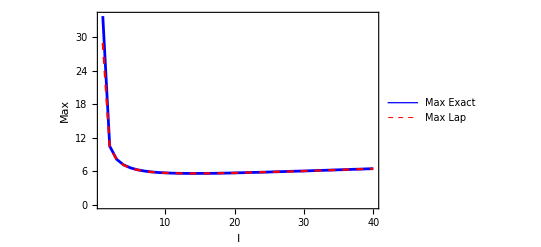

```mathematica
maxPy[k_,Inp_]:= Max[Function[y,p[y,Inp,k,V]/NIntegrate[p[yp,Inp,k,V],{yp,0,1}]]/@Range[0.005,0.995,0.01]];
maxPyLap[k_,Inp_]:= Max[Function[y,pLaplace[y,Inp,k,V]/NIntegrate[pLaplace[yp,Inp,k,V],{yp,0,1}]]/@Range[0.005,0.995,0.01]];
maxPyList[k_]:= Function[Inp,maxPy[k,Inp]]/@Range[0.005,0.995,0.025];
maxPyLapList[k_] := Function[Inp,maxPyLap[k,Inp]]/@Range[0.005,0.995,0.025];

ListLinePlot[{maxPyList[3],maxPyLapList[3]},PlotLegends->{"Max Exact","Max Lap" },PlotStyle->{{Thickness[0.005],Blue},{Red,Dashed,Thickness[0.004]}},TicksStyle->Directive["Label",30],Ticks->{Automatic},LabelStyle->{FontFamily->"Helvetica",FontSize->24},FrameLabel->{"I","Max"},Frame->True,FrameStyle->Directive[Black],PlotRange->All]
```

### Get Output Probability

0.998724

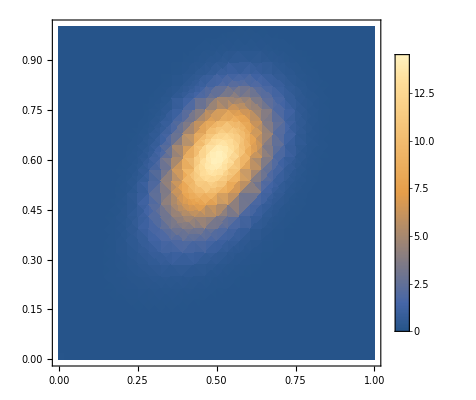

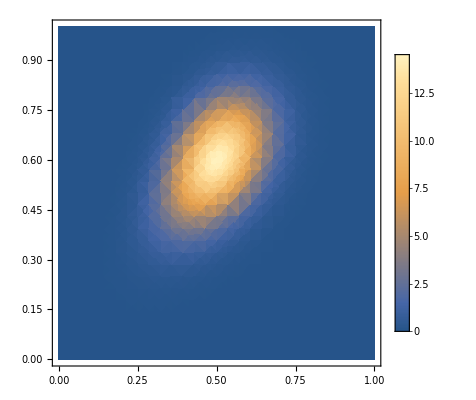

```mathematica
pInput[Inp_,mu_,sigma_]:= Exp[(-(Inp-mu)^2)/(2 sigma^2)]*1/((2 Pi sigma^2)^(1/2))      (* This probability is normalized *)
dx=0.1;
pLaplaceNormalized[y_,Inp_,k_,V_]:=Exp[V(1/2 fDoublePrimeyMax[Inp,k] (y-Omax[Inp,k])^2)](NIntegrate[pLaplace[yp,Inp,k,V],{yp,0.0001,1}])^-1
pOutputLap[y_,k_,V_]:=Sum[pLaplaceNormalized[y,Inp,k,V]*pInput[Inp,0.5,0.1]*dx,{Inp,0.0001,1,dx}]
pOutputLap1[y_,k_,V_]:=Sum[pLaplace[y,Inp,k,V]*pInput[Inp,0.5,0.1],{Inp,0.0001,1,dx}]
(* Sum[pOutputLap[y,k,V]*0.1,{y,0,1,0.1}] *)
 pNormalized[y_,Inp_,k_,V_]:=p[y,Inp,k,V](NIntegrate[p[yp,Inp,k,V],{yp,0.0001,1}])^-1 
pOutput[y_,k_,V_]:=Sum[pNormalized[y,Inp,k,V]*pInput[Inp,0.5,0.1]*dx,{Inp,0.0001,1,dx}]
pOutput1[y_,k_,V_]:=Sum[p[y,Inp,k,V]*pInput[Inp,0.5,0.1]*dx,{Inp,0.0001,1,dx}]
Sum[pNormalized[y,0.5,1.5,100]*0.1,{y,0,1,0.1}]

pJoint[y_,Inp_,k_,V_]:=pNormalized[y,Inp,k,V]*pInput[Inp,0.5,0.1]
pJointLaplace[y_,Inp_,k_,V_]:=pLaplaceNormalized[y,Inp,k,V]*pInput[Inp,0.5,0.1]
(* check to see if joint probabilities look similar *)
DensityPlot[{pJoint[y,x,k,V]},{x,0,1},{y,0,1},PlotRange->All,PlotLegends->Automatic]
DensityPlot[{pJointLaplace[y,x,k,V]},{x,0,1},{y,0,1},PlotRange->All,PlotLegends->Automatic]
```

#### Check that out probabilities match

```mathematica
lapList = Function[x,pOutputLap[x,k,V]]/@Range[0.005,0.995,0.01];
exactList = Function[x,pOutput[x,k,V]]/@Range[0.005,0.995,0.01];
```

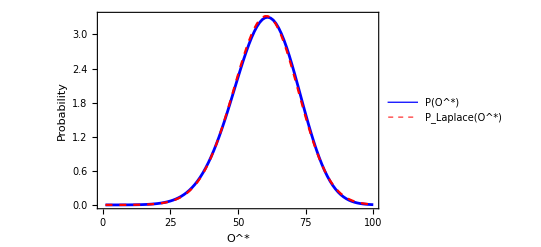

```mathematica
ListLinePlot[{exactList,lapList},PlotLegends->{"P(O^*)","P_Laplace(O^*)" },PlotStyle->{{Thickness[0.005],Blue},{Red,Dashed,Thickness[0.004]}},TicksStyle->Directive["Label",30],Ticks->{Automatic},LabelStyle->{FontFamily->"Helvetica",FontSize->24},FrameLabel->{"O^*","Probability "},Frame->True,FrameStyle->Directive[Black],PlotRange->All]
```

## Compute Mutual Information

```mathematica
(* Use java program to compute these integrals *)
```

```mathematica
MI[k_]:=Sum[pJoint[y,x,k,V]*Log[pJoint[y,x,k,V]/(pOutput[y,k,V]pInput[x,0.5,0.1])]*0.1*0.1,{x,0.01,1,0.1},{y,0.01,1,0.1}]
MILap[k_]:=Sum[pJointLaplace[y,x,k,V]*Log[pJointLaplace[y,x,k,V]/(pOutputLap[y,k,V]pInput[x,0.5,0.1])]*0.1*0.1,{y,0.01,1,0.1},{x,0.01,1,0.1}]

MI[3]
MILap[3]
```

0.0977908

0.0981962

```mathematica
V=20;
k=1.5;
MILoop = 0;
For[y=10^-6,y<1,y+=0.1,
For[
x=10^-6,x<1,x+=0.1,
(*Print[y," - ",x];*)
If[pJoint[y,x,k,V]>0,
MILoop +=pJoint[y,x,k,V]*Log[pJoint[y,x,k,V]/(pOutput[y,k,V]pInput[x,0.5,0.1])]*0.1*0.1;
(*Print[MILoop]*)
]
]
]
MILoop
```

0.294445

```mathematica
MIList = Function[k,MI[k]]/@Range[0.1,20,0.5];
(*MILapList = Function[k,MILap[k]]/@Range[0.1,50,0.5];*)
MILapList = Function[k,MILap[k]]/@Range[0.1,20,0.5]; 
(* ListPlot[{MIList,MILapList}] *)
(*ListPlot[{MIList,MILapList},PlotRange->All]*)
```

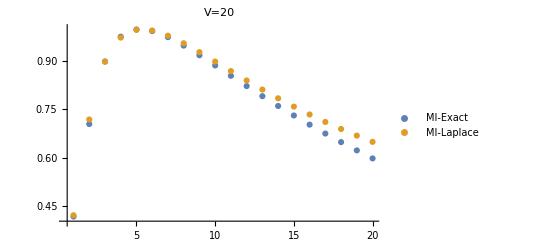

```mathematica
ListPlot[{MIList*10,MILapList*10},PlotRange->{{0.5,20},{0.4,1}},PlotLegends->{"MI-Exact","MI-Laplace"},PlotLabel->"V=20"]
```

## Under Development

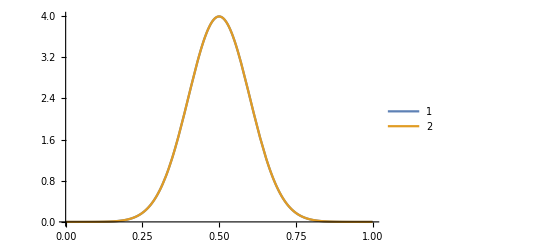
```mathematica
(* Compute MI 

pOutputLap[y_,k_,V_]:=NIntegrate[pLaplace[y,Inp,k,V]*pInput[Inp,0.5,0.1],{Inp,0,1}]
pJointApprox[y_,Inp_,k_,V_]:=pLaplace[y,Inp,k,V]*pInput[Inp,0.5,0.1]

pOutput[y_,k_,V_]:=NIntegrate[p[y,Inp,k,V]*pInput[Inp,0.5,0.1],{Inp,0,1}]
pJoint[y_,Inp_,k_,V_]:=p[y,Inp,k,V]*pInput[Inp,0.5,0.1]

MI[k_]:=Sum[Sum[pJoint[y,x,k]*Log[pJoint[y,x,k,V]/(pOutput[y,k,V]pInput[x,0.5,0.01])],{x,0.01,1,0.05}],{y,0.01,1, 0.05}]
MI[0.2]
$Aborted

MIList2 = Function[k,MI[k]]/@Range[0.5,5,0.5];


pIn = ProbabilityDistribution[pInput[x,0.5,0.1],{x,0,1},Method->"Normalize"]

Plot[{PDF[pIn,x],pInput[x,0.5,0.1]/nIn},{x,0,1},PlotRange->All,PlotLegends->Automatic]
ProbabilityDistribution[3.9894250911642475 ⅇ^(-49.99999999999999 (-0.5+x)^2),{x,0,1}]
-Graphics-
nIn = NIntegrate[pInput[x,0.5,0.1],{x,0,1}]
0.25066268375731465
Manipulate[
nOutLap = Sum[pOutputLap[y,k,V]*0.005,{y,0.0,1,0.005}];
nOut = Sum[pOutput[y,k,V]*0.005,{y,0,1,0.005}];
Plot[{pOutput[y,k,V]/nOut,pOutputLap[y,k,V]/nOutLap},{y,0.0,1},PlotRange->All],{V,1,1000}]

Sum[pOutputLap[y,k,V]*0.01/nOutLap,{y,0,1,0.01}]
1.0000000017787507
V=5
5 
Normalize via lists
dx=dy=0.1;
pNormalizedList[y_,Inp_,k_,V_]:=p[y,Inp,k,V](Total[Function[yp,p[yp,Inp,k,V]*dy]/@Range[0,1,dy]])^-1
(*Sum[pNormalizedList[y,Inp,k,V]*dy,{y,0,1,dy}]*) (* Output -> 1 *) 
pOutput[y_,k_,V_]:=Sum[pNormalizedList[y,Inp,k,V]*pInput[Inp,0.5,0.1]*dx,{Inp,10^-8,1,dx}]
(* Sum[pOutput[y,k,V]*dy,{y,0,1,dy}] Output -> 0.9999991426275873 *)
pJoint[y_,Inp_,k_,V_]:=pNormalizedList[y,Inp,k,V]*pInput[Inp,0.5,0.1]
(* Output probability as list *)
(*Column[Function[y,pOutput[y,0.2,5]]/@Range[0.005,0.995,0.1]]*)
(*Plot[pOutput[y,0.4,10],{y,0,1}]*)
*)
```